```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

Fitting model for CA

>> <|chiSquared→1.23663×10^-6,rmsRelativeError→0.318191,rmsRelativeErrorDeaths→0.22047,rmsRelativeErrorPcr→0.377495,meanRelativeErrorDeaths→-0.0576513,meanRelativeErrorPcr→0.010738,rSquaredDeaths→0.0300003,rSquaredPcr→0.00817335,deathResidual7Day→-0.212395,pcrResidual7Day→46.5326|>

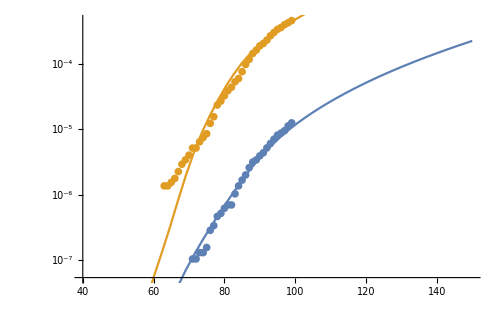
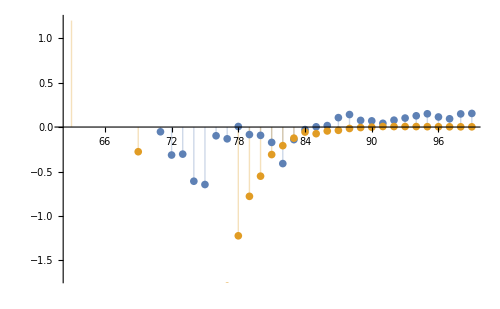
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.31568 | 0.284106 | 11.6706 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[11.6706,62.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 52.4603 | 1.80198 | 29.1127 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[29.1127,62.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 1.31303 | 0.0979278 | 13.4082 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[13.4082,62.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 1.57759 | 0.449377 | 3.51061 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[3.51061,62.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | 9.90521×10^-10 | 2.4763×10^-10
Error | 62 | 1.51141×10^-11 | 2.43776×10^-13
Uncorrected Total | 66 | 1.00563×10^-9 | 
Corrected Total | 65 | 9.87321×10^-10 |

>> scenario5

>> {3.31568,5,7,4,12,0.0480978,0.769564,4,10,0.357591,52.4603,3,12.5,730,0.901524,0.0742743,0.0242016,6925/38982847,0.000952557,1.31303,1.57759}

>> Current Indefinite scenario Generating simulations for CA in the

>> scenario1

>> {3.31568,5,7,4,12,0.0480978,0.769564,4,10,0.357591,52.4603,3,12.5,730,0.901524,0.0742743,0.0242016,6925/38982847,0.000952557,1.31303,1.57759}

>> Current scenario Generating simulations for CA in the

>> scenario2

>> {3.31568,5,7,4,12,0.0480978,0.769564,4,10,0.357591,52.4603,3,12.5,730,0.901524,0.0742743,0.0242016,6925/38982847,0.000952557,1.31303,1.57759}

>> Generating simulations for CA in the  Italy scenario

>> scenario3

>> {3.31568,5,7,4,12,0.0480978,0.769564,4,10,0.357591,52.4603,3,12.5,730,0.901524,0.0742743,0.0242016,6925/38982847,0.000952557,1.31303,1.57759}

>> Generating simulations for CA in the  Wuhan scenario

>> scenario4

>> {3.31568,5,7,4,12,0.0480978,0.769564,4,10,0.357591,52.4603,3,12.5,730,0.901524,0.0742743,0.0242016,6925/38982847,0.000952557,1.31303,1.57759}

>> Generating simulations for CA in the  Normal scenario

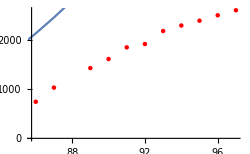
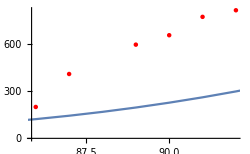
>> Current Hospitalizations for CA
-Graphics-Cumulative Hospitalizations for CA
-Graphics-Current ICU for CA
-Graphics-Cumulative ICU for CA
-Graphics-

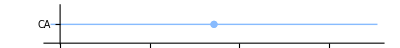
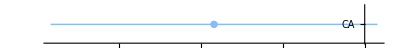
Currently Hospitalized
-Graphics- | Cumulative Hospitalized
-Graphics- | Currently ICU
-Graphics- | Cumulative ICU
-Graphics-

state | distancingLevel | id | distancingDays | maintain | name | summaryAug1 | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfSymptomaticHospitalized | fractionOfPCRHospitalized | fractionHospitalizedInICU | fractionOfInfectionsPCRConfirmed | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences"} |  | 
CA | 81/140 | scenario5 | 630 | True | Current Indefinite | <|"totalProjectedDeaths" -> 52778.88029695917, "totalProjectedPCRConfirmed" -> 1.0135878158433659*^6, "totalProjectedInfected" -> 5.365530126407809*^6, "totalInfectedFraction" -> 0.13763823166655348, "fatalityRate" -> 0.009836657152886834, "fatalityRateSymptomatic" -> 0.014052367361266905, "fatalityRatePCR" -> 0.05207134445775078, "fractionOfSymptomaticHospitalized" -> 0.10605252112502853, "fractionOfPCRHospitalized" -> 0.3929798599868359, "fractionHospitalizedInICU" -> 0.07197551680621335, "fractionOfInfectionsPCRConfirmed" -> 0.2698675731844911, "dateContained" -> "Thu 4 Mar 2021 00:00:00", "dateICUOverCapacity" -> "Wed 20 May 2020 11:33:24", "dateHospitalsOverCapacity" -> "Fri 29 May 2020 17:46:56"|> | 115558. | 3.14572×10^6 | 1.19177×10^7 | 0.305718 | 0.00969629 | 0.0138518 | 0.0367349 | 0.107833 | 0.285972 | 0.113834 | 0.377076 | Thu 4 Mar 2021 00:00:00 | Wed 20 May 2020 11:33:24 | Fri 29 May 2020 17:46:56 | 3.31568 | 52.4603 | 1.31303
CA | 81/140 | scenario1 | 90 | True | Current | <|"totalProjectedDeaths" -> 52599.05624464299, "totalProjectedPCRConfirmed" -> 1.7653736154032305*^6, "totalProjectedInfected" -> 9.245178373605086*^6, "totalInfectedFraction" -> 0.2371601636382557, "fatalityRate" -> 0.005689350071904821, "fatalityRateSymptomatic" -> 0.00812764295986403, "fatalityRatePCR" -> 0.029794858032150207, "fractionOfSymptomaticHospitalized" -> 0.10598908146073929, "fractionOfPCRHospitalized" -> 0.38854187501533166, "fractionHospitalizedInICU" -> 0.03987843571965297, "fractionOfInfectionsPCRConfirmed" -> 0.27278676579340905, "dateContained" -> "Wed 9 Dec 2020 00:00:00", "dateICUOverCapacity" -> "Wed 20 May 2020 11:33:24", "dateHospitalsOverCapacity" -> "Fri 29 May 2020 17:46:56"|> | 262499. | 9.54719×10^6 | 2.77939×10^7 | 0.712979 | 0.00944447 | 0.0134921 | 0.0274949 | 0.107697 | 0.21947 | 0.111331 | 0.490713 | Wed 9 Dec 2020 00:00:00 | Wed 20 May 2020 11:33:24 | Fri 29 May 2020 17:46:56 | 3.31568 | 52.4603 | 1.31303
CA | 0.4 | scenario2 | 90 | False | Italy | <|"totalProjectedDeaths" -> 8689.265848204195, "totalProjectedPCRConfirmed" -> 164173.3361409464, "totalProjectedInfected" -> 978351.2524244325, "totalInfectedFraction" -> 0.02509696771055312, "fatalityRate" -> 0.008881540067201325, "fatalityRateSymptomatic" -> 0.012687914381716178, "fatalityRatePCR" -> 0.05292738792092445, "fractionOfSymptomaticHospitalized" -> 0.10568060292557752, "fractionOfPCRHospitalized" -> 0.44084457842965497, "fractionHospitalizedInICU" -> 0.0037857883905318547, "fractionOfInfectionsPCRConfirmed" -> 0.2397230409456898, "dateContained" -> "Sat 19 Dec 2020 00:00:00", "dateICUOverCapacity" -> "Thu 13 Aug 2020 17:39:04", "dateHospitalsOverCapacity" -> "Thu 13 Aug 2020 16:19:53"|> | 255629. | 1.32571×10^7 | 2.96545×10^7 | 0.760707 | 0.00862023 | 0.0123146 | 0.0192823 | 0.108012 | 0.169127 | 0.102343 | 0.638647 | Sat 19 Dec 2020 00:00:00 | Thu 13 Aug 2020 17:39:04 | Thu 13 Aug 2020 16:19:53 | 3.31568 | 52.4603 | 1.31303
CA | 0.11 | scenario3 | 60 | False | Wuhan | <|"totalProjectedDeaths" -> 8013.589186456637, "totalProjectedPCRConfirmed" -> 220390.96426848884, "totalProjectedInfected" -> 1.1516220022396294*^6, "totalInfectedFraction" -> 0.02954176236126698, "fatalityRate" -> 0.006958523865358705, "fatalityRateSymptomatic" -> 0.009940748379083864, "fatalityRatePCR" -> 0.0363607882612382, "fractionOfSymptomaticHospitalized" -> 0.10440153131503191, "fractionOfPCRHospitalized" -> 0.38187486792063374, "fractionHospitalizedInICU" -> 0.004049766889811859, "fractionOfInfectionsPCRConfirmed" -> 0.27339199325557606, "dateContained" -> "Mon 18 May 2020 00:00:00", "dateICUOverCapacity" -> "Sun 16 Aug 2020 01:11:14", "dateHospitalsOverCapacity" -> "Sat 15 Aug 2020 22:27:59"|> | 263877. | 1.39782×10^7 | 3.0098×10^7 | 0.772084 | 0.00876726 | 0.0125247 | 0.0188777 | 0.10761 | 0.162194 | 0.104255 | 0.663462 | Mon 18 May 2020 00:00:00 | Sun 16 Aug 2020 01:11:14 | Sat 15 Aug 2020 22:27:59 | 3.31568 | 52.4603 | 1.31303
CA | 1 | scenario4 | 90 | False | Normal | <|"totalProjectedDeaths" -> 273786.327900419, "totalProjectedPCRConfirmed" -> 4.376606698822694*^6, "totalProjectedInfected" -> 2.877358126142888*^7, "totalInfectedFraction" -> 0.7381087702862975, "fatalityRate" -> 0.009515198174772593, "fatalityRateSymptomatic" -> 0.013593140249675133, "fatalityRatePCR" -> 0.06255675840693373, "fractionOfSymptomaticHospitalized" -> 0.1077397375884392, "fractionOfPCRHospitalized" -> 0.49582720485117526, "fractionHospitalizedInICU" -> 0.11421265396686542, "fractionOfInfectionsPCRConfirmed" -> 0.21729291280170435, "dateContained" -> "Fri 4 Sep 2020 00:00:00", "dateICUOverCapacity" -> "Thu 30 Apr 2020 14:04:30", "dateHospitalsOverCapacity" -> "Thu 30 Apr 2020 17:08:04"|> | 276636. | 4.39553×10^6 | 2.88198×10^7 | 0.739295 | 0.00959881 | 0.0137126 | 0.0629358 | 0.107694 | 0.494276 | 0.112948 | 0.217882 | Fri 4 Sep 2020 00:00:00 | Thu 30 Apr 2020 14:04:30 | Thu 30 Apr 2020 17:08:04 | 3.31568 | 52.4603 | 1.31303

```mathematica
asd=GenerateModelExport[10,{"CA"}];
TableForm[Import["tests/summary.csv"]]
```

```mathematica
tempParams={3.315677597140117,5,7,4,12,0.0480977695615949,0.7695643129855184,4,10,0.3575906619299291,52.460287850366974,3,12.5,730,0.9015240847617458,0.07427433850312418,0.024201576735129928,6925/38982847,0.0009525570076091405,1.3130347650158096,1.5775877732714718}
```

{3.31568,5,7,4,12,0.0480978,0.769564,4,10,0.357591,52.4603,3,12.5,730,0.901524,0.0742743,0.0242016,6925/38982847,0.000952557,1.31303,1.57759}

```mathematica
m=integrateModel[
stateDistancingPrecompute["CA"]["scenario1"]["distancingFunction"],
tempParams
];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{herd,{{223.306,0.7}}},{icu,{{141.646,0.000177642}}},{hospital,{{150.909,0.000952557}}}}

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
sol=Apply[m,tempParams];
sol[[1]];
s = Sum[s[#],{s,sol[[1]]}]&
s[250]
```

∑_s^sol⟦1⟧ s[#1]&

0.2934